## <r^2(t)>, calcul numérique

### États propres dans la base atomique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* états propres et leurs énergies dans la base atomique *)
valvec[vv_,rr_]:=Block[{v=vv,r=rr,i=5},
Eigensystem[h[i]]
]
```

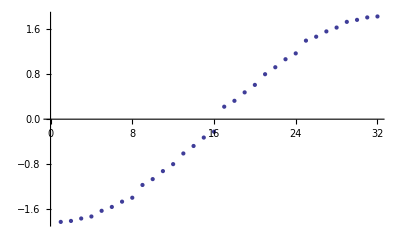

```mathematica
(* le spectre est bien comme on l'attend *)
ListPlot[Sort[valvec[.9,.9][[1]]]]
```

```mathematica
(* les vecteurs propres sont bien normalisés à 1 *)
Norm/@valvec[.1,.001][[2]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Propagateur retardé dans la base atomique

### <r^2(t)>_n